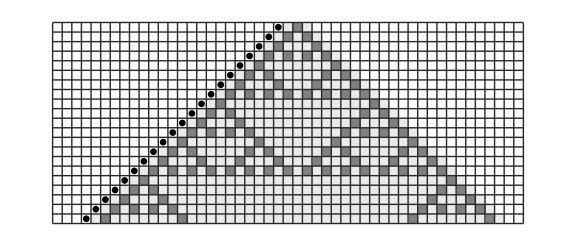
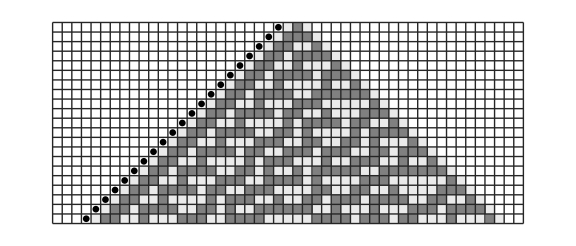

```mathematica
CAToMA[rule_]:=With[{rules=#->CellularAutomaton[rule,#][[2]]&/@Tuples[{1,0},3],numbermap=<|B->0,Y[1]->6,Y[0]->1,X[0,0]->2,X[0,1]->3,X[1,0]->4,X[1,1]->5|>},#->(#/.{{X[a_,b_],Y[c_],Y[d_]}:>{X[c,{a,c,d}/.rules],1},{X[a_,b_],Y[c_],B}:>{X[c,{a,c,0}/.rules],1},{_X,B,B}:>{Y[0],-1},{_X,X[_,a_],_Y}:>{Y[a],-1},{B,X[_,a_],_Y}:>{Y[a],-1},{B,B,_Y}:>{X[0,0],1},_:>{B,0}})&/@Tuples[Keys[numbermap],3]/.numbermap];

Table[ResourceFunction["MobileAutomatonPlot"][Module[{min=Infinity},Select[If[#[[2]]<min,min=#[[2]];True,False]&]]@ResourceFunction["MobileAutomaton"][CAToMA[ruleN],{CenterArray[{0,0,1,6,1},49],24},940],],{ruleN,{90,30}}]
```